```mathematica
cancerFile = FileNameJoin[{NotebookDirectory[],"kNN/tune_k_and_p.cancer.precis.dat"}];
glassFile = FileNameJoin[{NotebookDirectory[],"kNN/tune_k_and_p.glass.precis.dat"}];
irisFile = FileNameJoin[{NotebookDirectory[],"kNN/tune_k_and_p.iris.precis.dat"}];
soybeanFile = FileNameJoin[{NotebookDirectory[],"kNN/tune_k_and_p.soybean.precis.dat"}];
voteFile = FileNameJoin[{NotebookDirectory[],"kNN/tune_k_and_p.vote.precis.dat"}];
```

```mathematica
cancerData=ReadList[cancerFile,Number,RecordLists->True];
glassData=ReadList[glassFile,Number,RecordLists->True];
irisData=ReadList[irisFile,Number,RecordLists->True];
soybeanData=ReadList[soybeanFile,Number,RecordLists->True];
voteData=ReadList[voteFile,Number,RecordLists->True];
```

```mathematica
ListPointPlot3D[cancerData,PlotStyle->PointSize[Large]]
ListPointPlot3D[glassData,PlotStyle->PointSize[Large]]
ListPointPlot3D[irisData,PlotStyle->PointSize[Large]]
ListPointPlot3D[soybeanData,PlotStyle->PointSize[Large]]
ListPointPlot3D[voteData,PlotStyle->PointSize[Large]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

```mathematica
kmin=1;
kmax=20;
kr =kmax -kmin;
pmin=1;
pmax=10;
pr = pmax - pmin;
```

```mathematica
cancerDataOrg = Array[{},{kmax,pmax}];
glassDataOrg = Array[{},{kmax,pmax}];
irisDataOrg = Array[{},{kmax,pmax}];
soybeanDataOrg = Array[{},{kmax,pmax}];
voteDataOrg = Array[{},{kmax,pmax}];
aveDataOrg= Array[{},{kmax,pmax}];
```

```mathematica
For[i = kmin, i < kmax,i++,
For[j = pmin, j < pmax, j++,
For[k = 1, k <= Length[cancerData], k++,
If[cancerData[[k,1]]==i∧cancerData[[k,2]]==j,
cancerDataOrg[[i,j,0]]=Append[cancerDataOrg[[i,j,0]],cancerData[[k,3]]];
aveDataOrg[[i,j,0]]=Append[aveDataOrg[[i,j,0]],cancerData[[k,3]]];
];
If[glassData[[k,1]]==i∧glassData[[k,2]]==j,
glassDataOrg[[i,j,0]]=Append[glassDataOrg[[i,j,0]],glassData[[k,3]]];
aveDataOrg[[i,j,0]]=Append[aveDataOrg[[i,j,0]],glassData[[k,3]]];
];
If[irisData[[k,1]]==i∧irisData[[k,2]]==j,
irisDataOrg[[i,j,0]]=Append[irisDataOrg[[i,j,0]],irisData[[k,3]]];
aveDataOrg[[i,j,0]]=Append[aveDataOrg[[i,j,0]],irisData[[k,3]]];
];
If[soybeanData[[k,1]]==i∧soybeanData[[k,2]]==j,
soybeanDataOrg[[i,j,0]]=Append[soybeanDataOrg[[i,j,0]],soybeanData[[k,3]]];
aveDataOrg[[i,j,0]]=Append[aveDataOrg[[i,j,0]],soybeanData[[k,3]]];
];
If[voteData[[k,1]]==i∧voteData[[k,2]]==j,
voteDataOrg[[i,j,0]]=Append[voteDataOrg[[i,j,0]],voteData[[k,3]]];
aveDataOrg[[i,j,0]]=Append[aveDataOrg[[i,j,0]],voteData[[k,3]]];
];
]
]
]
```

```mathematica
cancerDataAve = {};
glassDataAve = {};
irisDataAve={};
soybeanDataAve={};
voteDataAve={};
aveDataAve = {};
```

```mathematica
For[i = kmin, i < kmax,i++,
For[j = pmin, j < pmax, j++,
AppendTo[cancerDataAve,{i,j,Mean[cancerDataOrg[[i,j,0]]]}];
AppendTo[glassDataAve,{i,j,Mean[glassDataOrg[[i,j,0]]]}];
AppendTo[irisDataAve,{i,j,Mean[irisDataOrg[[i,j,0]]]}];
AppendTo[soybeanDataAve,{i,j,Mean[soybeanDataOrg[[i,j,0]]]}];
AppendTo[voteDataAve,{i,j,Mean[voteDataOrg[[i,j,0]]]}];
AppendTo[aveDataAve,{i,j,Mean[aveDataOrg[[i,j,0]]]}];
]
]
```

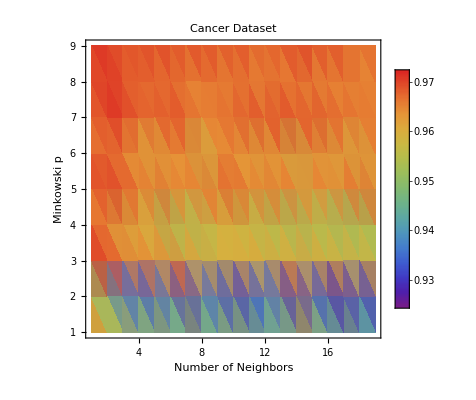

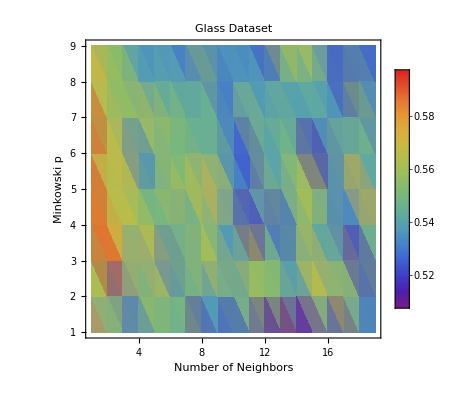

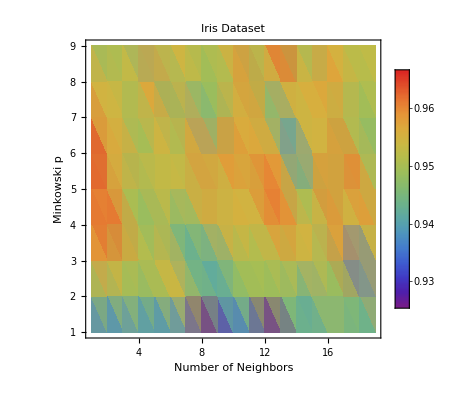

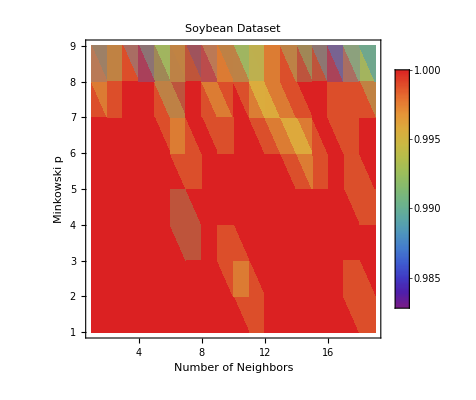

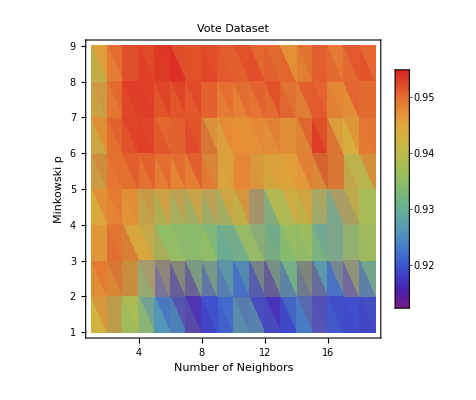

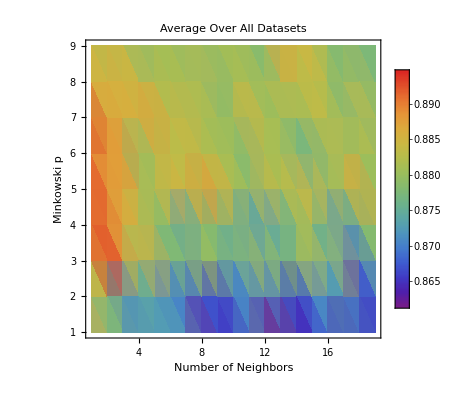

```mathematica
ListDensityPlot[cancerDataAve,PlotLabel->"Cancer Dataset",FrameLabel->{"Number of Neighbors","Minkowski p"},ColorFunction->"Rainbow",PlotLegends->Automatic]
ListDensityPlot[glassDataAve,PlotLabel->"Glass Dataset",FrameLabel->{"Number of Neighbors","Minkowski p"},ColorFunction->"Rainbow",PlotLegends->Automatic]
ListDensityPlot[irisDataAve,PlotLabel->"Iris Dataset",FrameLabel->{"Number of Neighbors","Minkowski p"},ColorFunction->"Rainbow",PlotLegends->Automatic]
ListDensityPlot[soybeanDataAve,PlotLabel->"Soybean Dataset",FrameLabel->{"Number of Neighbors","Minkowski p"},ColorFunction->"Rainbow",PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[voteDataAve,PlotLabel->"Vote Dataset",FrameLabel->{"Number of Neighbors","Minkowski p"},ColorFunction->"Rainbow",PlotLegends->Automatic]
ListDensityPlot[aveDataAve,PlotLabel->"Average Over All Datasets",FrameLabel->{"Number of Neighbors","Minkowski p"},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
Position[aveDataAve,Max[aveDataAve[[1]]]]
```

{{1,1},{1,2},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,2},{19,2},{28,2},{37,2},{46,2},{55,2},{64,2},{73,2},{82,2},{91,2},{100,2},{109,2},{118,2},{127,2},{136,2},{145,2},{154,2},{163,2}}